## Tarea 2 - Andrey Arguedas Espinoza - 2020426569

La canica entra por A o por B
La canica cae por X1 hacia la izquierda, la canica se va a C
La canica cae por X1 hacia la derecha, la canica se va a X2
La canica cae por x2 hacia la izquierda desde X1, la canica se va a C
La canica cae por x2 hacia la derecha desde X1, la canica se va a D
La canica cae por X3 hacia la derecha, la canica se va a D
La canica cae por X3 hacia la izquierda, la canica se va a X2
La canica cae por X2 hacia la izquierda desde X3, la canica se va a C
La canica cae por X2 hacia la derecha desde X3, la canica se va a D

## Programación del automata Primero cambiaremos el grafo anterior por números para que sea más sencillo de visualizar en Mathematica -Graphics- Comenzamos a programar la función Delta Hat y definimos la asociación

```mathematica
DeltaHat[δ_,q0_,string_]:=FoldList[δ[{#1,#2}]&,q0,Characters[string]]
```

```mathematica
δ=Association[
{0,"0"}->1,
{0,"1"}->2,
{1,"0"}->3,
{1,"1"}->4,
{3,"0"}->5,
{3,"1"}->5,
{4,"0"}->6,
{4,"1"}->7,
{6,"0"}->5,
{6,"1"}->5,
{2,"0"}->8,
{2,"1"}->9,
{9,"0"}->10,
{9,"1"}->10,
{8,"0"}->6,
{8,"1"}->7,
{7,"0"}->10,
{7,"1"}->10,
{5,"0"}->5,
{5,"1"}->5,
{10,"0"}->10,
{10,"1"}->10
];
```

```mathematica
DeltaHat[δ, 0, "000"]
```

{0,1,3,5}

```mathematica
DeltaHat[δ, 0, "111"]
```

{0,2,9,10}

```mathematica
DeltaHat[δ, 0, "1011"]
```

{0,2,8,7,10}

```mathematica
IsValid[δ_, q0_,qf_, string_] := Fold[δ[{#1, #2}]&, q0,Characters[string]] == qf;
```

```mathematica
Tally[Map[IsValid[δ,0,10,#]&,Map[StringJoin,Tuples[{"0","1"},3]]]]
```

{{False,6},{True,2}}

## Build a Graph Representation

```mathematica
ToEdges[δ_]:=MapThread[DirectedEdge,{First/@Keys[δ],Values[δ]}];
ToVertexLabels[s_]:=Table[Rule[i-1,Placed[i-1,Center]],{i,1,s}];
ToEdgeLabels[δ_]:=MapThread[Rule,{ToEdges[δ],Last/@Keys[δ]}];
UnifyLabels[labels_]:=If[Length[#]>1,First[Keys[#]]->(Values[#]&/@#),First[#]]&/@GatherBy[labels,First];
UnifyEdges[edges_]:=First/@Gather[edges];
ShowGraph[δ_,s_,q0_,q_List]:=Graph[UnifyEdges[ToEdges[δ]],VertexSize->Large,VertexLabels->ToVertexLabels[s],EdgeLabels->UnifyLabels[ToEdgeLabels[δ]],VertexStyle->Join[{0->White},Map[(#->Red)&,q]]]
```

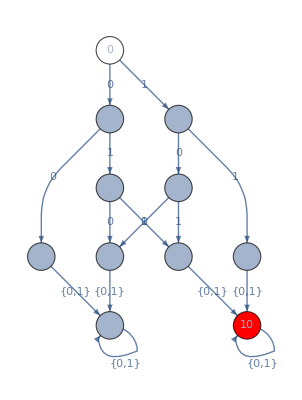

```mathematica
ShowGraph[δ,11,0,{10}]
```

## Como cambiaría el apartado A

## Como cambiaría el apartado B

La canica entra por A o por B
La canica cae por X1 hacia la izquierda, X1 cambia y la canica se va a X2
La canica cae por X1 hacia la derecha, X1 cambia y la canica se va a C
La canica cae por x2 hacia la izquierda desde X1, X2 cambia y la canica se va a D
La canica cae por x2 hacia la derecha desde X1, X2 cambia y la canica se va a C
La canica cae por X3 hacia la derecha, X3 cambia y la canica se va a X2
La canica cae por X3 hacia la izquierda, X3 cambia y la canica se va a D
La canica cae por X2 hacia la izquierda desde X3, X2 cambia y la canica se va a D
La canica cae por X2 hacia la derecha desde X3, X2 cambia y la canica se va a D

## Programación del automata con los cambios solicitados

```mathematica
δ=Association[
{0,"0"}->1,
{0,"1"}->2,
{1,"0"}->4,
{1,"1"}->3,
{3,"0"}->5,
{3,"1"}->5,
{4,"0"}->7,
{4,"1"}->6,
{6,"0"}->5,
{6,"1"}->5,
{2,"0"}->9,
{2,"1"}->8,
{9,"0"}->10,
{9,"1"}->10,
{8,"0"}->7,
{8,"1"}->6,
{7,"0"}->10,
{7,"1"}->10,
{5,"0"}->5,
{5,"1"}->5,
{10,"0"}->10,
{10,"1"}->10
];
```

```mathematica
DeltaHat[δ, 0, "0011"]
```

{0,1,4,6,5}

```mathematica
DeltaHat[δ, 0, "1100"]
```

{0,2,8,7,10}

```mathematica
Tally[Map[IsValid[δ,0,10,#]&,Map[StringJoin,Tuples[{"0","1"},3]]]]
```

{{False,6},{True,2}}

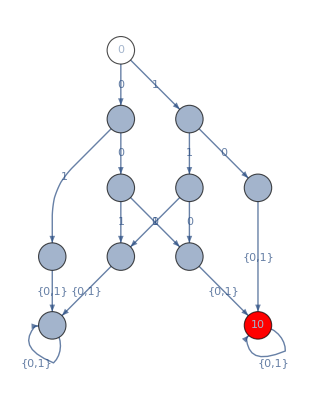

```mathematica
ShowGraph[δ,11,0,{10}]
```